```mathematica
UNET`$Verbose=True;
<<UNET`
```

True

--------------------------------------

Loading UNET` with version number 1.2.3

--------------------------------------

Defined packages and functions to be loaded are:

- UNET`UnetCore` with functions:

{AddLossLayer,AugmentTrainData,BlockType,BrierLossLayer,ClassDecoder,ClassEncoder,ClassScale,DiceSimilarity,DiceSimilarityClass,DropOutRate,MakeChannelImage,MakeClassImage,MakeDifferenceImage,MakeDiffLabel,MakeNetPlots,MakeUNET,NetLossLayers,NetParameters,NumberRowItems,RandomizeSplit,RotateFlip,ShowChannelClassData,SoftDiceLossLayer,SplitRatios,SplitTrainData,StepSize,TrainUNET,VisualizeUNET2D}

- UNET`UnetSupport` with functions:

{CreateImage1,CreateImage2,CreateImage3,CreateImage4,MakeTestImages}

--------------------------------------

Removing all local and global definitions of:

- UNET`UnetCore`

- UNET`UnetSupport`

--------------------------------------

Loading and protecting all definitions of:

- UNET`UnetCore`

- UNET`UnetSupport`

## Generated Data

### Show 2D UNET

```mathematica
dim={112,112};
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UNET"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UResNet"]
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"ResNet"]
```

```mathematica
MakeUNET[1,8,{4,2},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[1,8,{4,2},{128,128},DropOutRate->.5,BlockType->"DenseNet"]
```

### Show 3D UNET

```mathematica
dim={32,112,112};
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UNET"]
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UResNet"]
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"ResNet"]
```

```mathematica
MakeUNET[1,8,{4,2},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[1,8,{4,2},{128,128},DropOutRate->.5,BlockType->"DenseNet"]
```

### Describe UNET

```mathematica
style={Bold,TextAlignment->Center,FontFamily->"Helvetica"};
lab=Style[#,style]&/@{"n or (n, r)", "Unet", "UResNet", "ResNet", "UDenseNet", "DenseNet"};
```

```mathematica
CountConv=Count[Head/@Information[#,"LayersList"],ConvolutionLayer]&;
```

```mathematica
(*parameters*)
dim2D={112,112};
dim3D={32,112,112};
{nchan,nclass}={4,8};

dep={8,16,24,32,48,64};
depD={{2,4},{4,4},{6,4},{8,4},{12,4},{16,4}};
par=Table[ToString[dep[[i]]]<>" or ("<>ToString[depD[[i,1]]]<>","<>ToString[depD[[i,2]]]<>")",{i,1,Length[dep]}];
```

```mathematica
(*2D UNET generation*)
par2D=Table[
nets2D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim2D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets2D}
,{i,1,Length[dep]}];

tab1=Column[{Style["2D Nets - Numer of Array Elementes",style],TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
(*3D UNET generation*)
par3D=Table[nets3D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim3D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets3D}
,{i,1,Length[dep]}];

tab2=Column[{Style["3D Nets - Numer of Array Elementes",style],TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
layers2D=ToString[CountConv[#]]&/@nets2D;
layers3D=ToString[CountConv[#]]&/@nets3D;
layers=Column[{Style["Number of convolution layers",style],Style["1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style]},Alignment->Center];
```

```mathematica
Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1,order1}=SplitTrainData[data1,label1];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*visualize the test data*)
ShowChannelClassData[testData1,testLabel1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->2]
```

-Graphics- | -Graphics- | -Graphics-

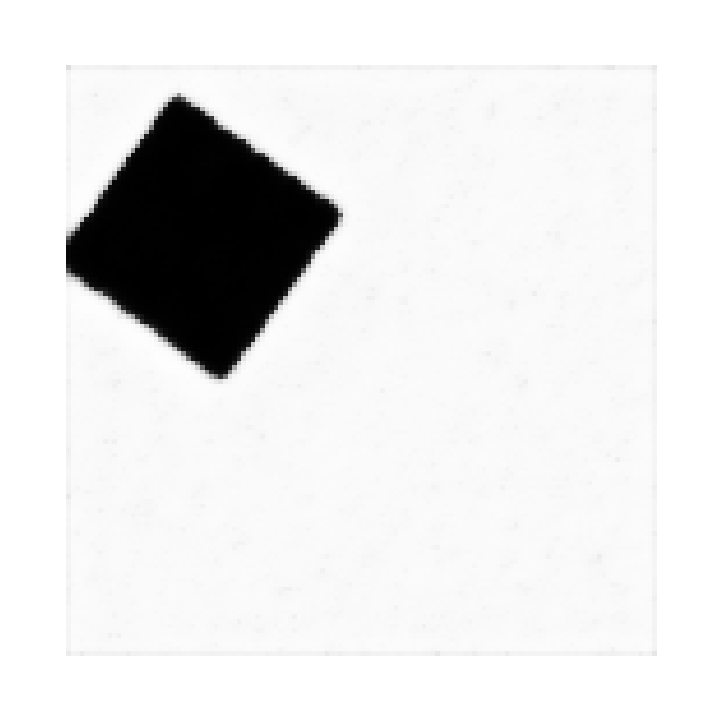

```mathematica
ArrayPlot@netTrained1[testData1[[1]]]
```

```mathematica
trained1["TrainingNet"]
```

NetGraph[<>]

channels: 1 - classes: 1 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.997}

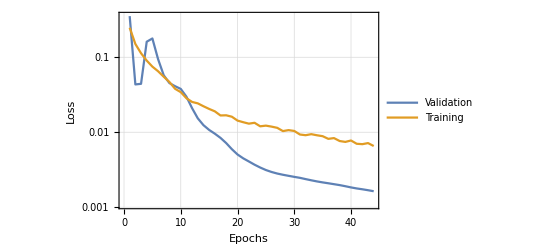
{-Graphics-,-Graphics-}

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->16,DropOutRate->.5];
MakeNetPlots[trained1]
```

```mathematica
Dimensions[testData2[[1]]]
```

{1,128,128}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2,order}=SplitTrainData[data2,label2];
```

Nuber of Samples in each set: {70,20,10}

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

NetGraph[<>]

```mathematica
netTrained2[testData2[[1]]]
```

```mathematica
test=netTrained2[testData2[[1]]];
Dimensions[test]
testl=ClassEncoder[testLabel2[[1]],2];
Dimensions[testl]
```

{128,128,2}

{128,128,2}

```mathematica
Total[Flatten[test]] Total[Flatten[testl]]
```

2.68435×10^8

0.0600876

```mathematica
sd=NetExtract[trained2["TrainedNet"],{"SoftDice"}]
```

NetGraph[<>]

```mathematica
i=1;
```

```mathematica
N@DiceDissimilarity[Flatten@Round[test],Flatten@Round[testl]]
```

0.00646973

```mathematica
DiceSimilarity
```

```mathematica
Column@Table[
{test,testl}={netTrained2[testData2[[i]]],ClassEncoder[testLabel2[[i]],2]};
{
sd[{test,testl}],
N@DiceDissimilarity[Flatten@Round[test],Flatten@Round[testl]],
1.-(2Total[Flatten[Round[test] testl]]/(Total[Flatten[Round[test]]]+Total[Flatten[testl]])),
1-(2Total[Flatten[test testl]]/(Total[Flatten[test]]+Total[Flatten[testl]]))

}
,{i,1,Length@testData2}]
```

{0.0750325,0.00701904,0.00701904,0.0600876}
{0.138349,0.00372314,0.00372314,0.0676605}
{0.066135,0.00616455,0.00616455,0.0580035}
{0.177248,0.00366211,0.00366211,0.0692038}
{0.0626229,0.00695801,0.00695801,0.0567843}
{0.172893,0.00366211,0.00366211,0.0692831}
{0.134315,0.00439453,0.00439453,0.0679205}
{0.0808086,0.00463867,0.00463867,0.0603401}
{0.120744,0.00408936,0.00408936,0.0658935}
{0.130283,0.00646973,0.00646973,0.0683221}

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.997,2→0.985}

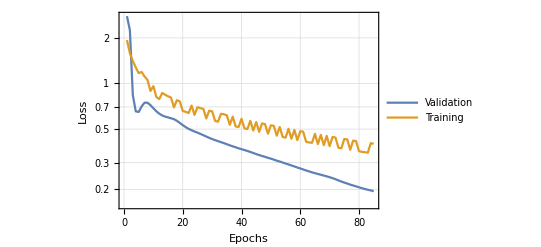
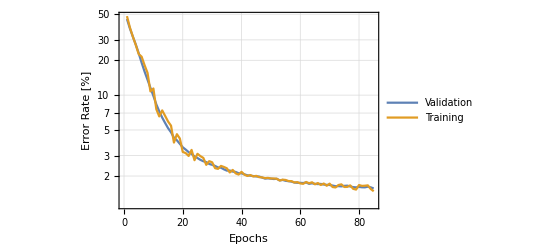

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},BatchSize->50,
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->4,DropOutRate->0.5,WorkingPrecision->"Mixed",PerformanceGoal->"TrainingMemory"];
MakeNetPlots[trained2]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[150,3];
```

```mathematica
(*data augmentation, increase the data by flipping and rotating*)
(*visualize the flips and rotations*)
data3R=RotateFlip[data3[[1;;2]]];
label3R=RotateFlip[label3[[1;;2]]];
ShowChannelClassData[data3R,label3R, NumberRowItems->4,MakeDifferenceImage->False,StepSize->1,ImageSize->200]
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3,order3}=SplitTrainData[data3,label3,AugmentTrainData->True];
```

Dimensions data: {150,1,128,128} - Dimensions label: {150,128,128}

Nuber of Samples in each set: {105,30,15}

Nuber of Samples in each set afeter augmentation: {840,240,15}

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},BatchSize->30,
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->32,BlockType->"ResNet",DropOutRate->0.25];
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4,order4}=SplitTrainData[data4,label4];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData4
```

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
TargetDevice->{"GPU",1},MaxTrainingRounds->50,NetParameters->32,BlockType->"ResNet",DropOutRate->0.5];
```

```mathematica
MakeNetPlots[trained4]
```

```mathematica
MeanSurfaceDistance[res_,label_]:=Block[{resS,labS,posR,posL,m,pR,pL,mat,msd,lpR,lpL},
(*Split the segmentations*)
resS=SplitSegmentations[res][[1]];
labS=SplitSegmentations[label][[1]];
(*Get the posisitons of the edge voxels*)
posR=aa=Map[Position[m=ArrayPad[#,1];m1=m-Erosion[m,1],1]&,resS,{2}];
posL=bb=Map[Position[m=ArrayPad[#,1];m2=m-Erosion[m,1],1]&,labS,{2}];
(*calculate the MSD for each point for ech ROI*)
msd=MapThread[(
pR=#;pL=#2;
lpR=Length[pR];lpL=Length[pL];
If[lpR==0||lpL==0,
Missing,
msd=ParallelMap[Norm[Nearest[pL,#,1][[1]]-#]&,pR];
Mean[N[msd]]
]
)&,{posR,posL},2];

Mean[DeleteCases[#,Missing]]&/@Transpose[msd]
]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5,order}=SplitTrainData[data5,label5];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

```mathematica
im=3;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;

(*train the net with monitor function*)
{{net,trained,netTrained},{result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5},BatchSize->15,
 TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->8,DropOutRate->.5,
BlockType->"ResNet",TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Rounds"]}];
```

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.999,2→0.983,3→0.996,4→0.984}

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];
```

```mathematica
(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```